## Toy 1

```mathematica
Clear[κ,ω0,ω1,ω2,ω3]
Ω=({{ω0, κ, 0}, {κ, ω1, κ}, {0, κ, ω2}});
ωb1=Eigenvalues[Ω][[2]]
ωb2=Eigenvalues[Ω][[1]]
ωb3=Eigenvalues[Ω][[3]]
```

Root[κ^2 ω0+κ^2 ω2-ω0 ω1 ω2+(-2 κ^2+ω0 ω1+ω0 ω2+ω1 ω2) #1+(-ω0-ω1-ω2) #1^2+#1^3&,2]

Root[κ^2 ω0+κ^2 ω2-ω0 ω1 ω2+(-2 κ^2+ω0 ω1+ω0 ω2+ω1 ω2) #1+(-ω0-ω1-ω2) #1^2+#1^3&,1]

Root[κ^2 ω0+κ^2 ω2-ω0 ω1 ω2+(-2 κ^2+ω0 ω1+ω0 ω2+ω1 ω2) #1+(-ω0-ω1-ω2) #1^2+#1^3&,3]

```mathematica
SetOptions[Plot,{Frame->True,FrameLabel->{"δ","ω"}}];
```

#### Caso degerado

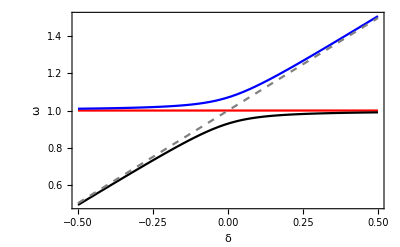

```mathematica
rnum={ω0-> 1.0,ω1-> 1.0+δ,ω2-> 1.0,κ-> 0.05};
Plot[{ωb1,ωb2,ωb3,ω1}/.rnum//Evaluate,{δ,-0.5,0.5},PlotStyle->{Red,Black,Blue,{Gray,Dashed}}]
```

#### Caso não-degerado 1

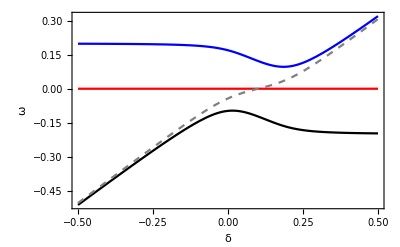

```mathematica
rnum={ω0-> 0.8,ω1-> 0.8+δ,ω2-> 1.0,κ-> 0.05};
Plot[({ωb1,ωb2,ωb3,ω1}-ωb1)//.rnum//Evaluate,{δ,-0.5,0.5},PlotStyle->{Red,Black,Blue,{Gray,Dashed}}]
```

#### Caso não-degerado 2

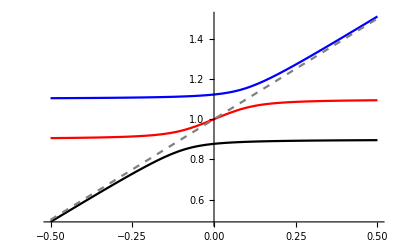

```mathematica
rnum={ω0-> 0.9,ω1-> 1.0+δ,ω2-> 1.1,κ-> 0.05};
Plot[{ωb1,ωb2,ωb3,ω1}/.rnum//Evaluate,{δ,-0.5,0.5},PlotStyle->{Red,Black,Blue,{Gray,Dashed}}]
```

#### a

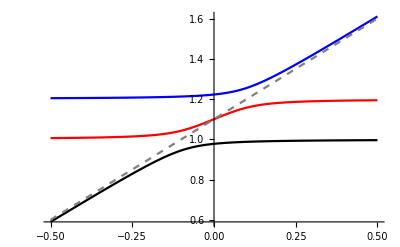

## Toy 2

```mathematica
ClearAll[κ,ω0,ω1,ω2,ω3,Ω]
Ω[μ_,ω0_,D1_,D2_]:=({{ω1[μ,ω0,D1⟦1⟧,D2⟦1⟧], κ[μ], 0}, {κ[μ], ω2[μ,ω0,D1⟦2⟧,D2⟦2⟧], κ[μ]}, {0, κ[μ], ω3[μ,ω0,D1⟦3⟧,D2⟦3⟧]}});
```

```mathematica
ω1[μ_,ω0_,D10_,D20_]:=ω0[[1]]+D10*μ+D20/2 μ^2;
ω2[μ_,ω0_,D10_,D20_]:=ω0[[2]]+D10*μ+D20/2 μ^2;
ω3[μ_,ω0_,D10_,D20_]:=ω0[[3]]+D10*μ+D20/2 μ^2;
Ω[μ,{0.1,0.1,0.1},{0,0,0}]
```

Ω[μ,{0.1,0.1,0.1},{0,0,0}]

```mathematica
Eigenvalues[Ω[μ,{0,0},{0.1,0.1,0.1},{0,0,0}]][[2]]/.{ω0->0,κ[μ]->0.05}
```

Root[0.+0.0005 μ-0.001 μ^3+(-0.005+0.03 μ^2) #1-0.3 μ #1^2+#1^3&,2]

```mathematica
Ω[μ,{0,0,0},{0.1,0.1,0.1},{0,0,0}]
```

Ω[μ,{0,0,0},{0.1,0.1,0.1},{0,0,0}]

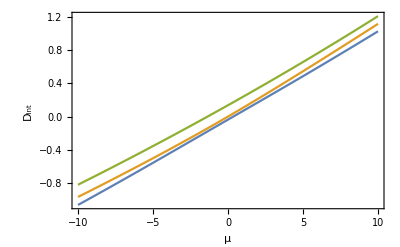

```mathematica
plt1=Plot[Eigenvalues[Ω[μ,{0,0.1,0},{0.15,0.1,0.1},{0,0,0}]]/.{κ[μ]->0.0}//Evaluate,{μ,-10,10},PlotStyle->{{Dashed,Black,Thick},{Dashed,Black,Thick},{Dashed,Black,Thick}}];
plt2=Plot[Eigenvalues[Ω[μ,{0,0.1,0},{0.11,0.1,0.1},{10^-3,10^-3,10^-3}]]/.{κ[μ]->0.05}//Evaluate,{μ,-10,10}];
Show[plt2]
```

```mathematica
(10. 10^9)/(193 10^12)
```

0.0000518135

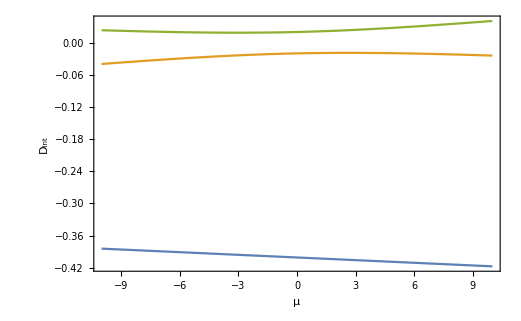

```mathematica
SetOptions[Plot,{Frame->True,FrameLabel->{"μ","D_int"}}];
ω0vec={-0.4,0.0,0};
D1vec={0.1,.105,0.1};
D2vec=-{10^-3,10^-3,10^-3};
sty={{Dashed,Gray},{Dashed,Gray},{Dashed,Gray}};
plt1=Plot[Eigenvalues[Ω[μ,ω0vec,D1vec-Mean[D1vec],D2vec-Mean[D2vec]]]/.{κ[μ]->0}//Evaluate,{μ,-10,10},PlotStyle->sty];
plt2=Plot[Eigenvalues[Ω[μ,ω0vec,D1vec-Mean[D1vec],D2vec-D2vec⟦3⟧]]/.{κ[μ]->0.02+ 0 1 10^-2 Exp[-μ/10]}//Evaluate,{μ,-10,10}];
Show[plt2]
```

```mathematica
c0=3. 10^8
R0=50 10^-6;
D10=c0/(2.1*2*π R0)*10^-9
D20=-15. 10^6 10^-9
```

3.×10^8

454.728

-0.015

5

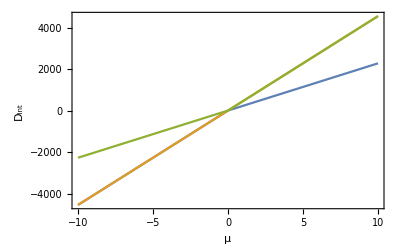

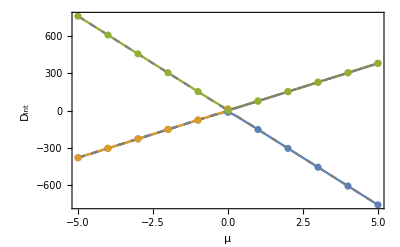

```mathematica
SetOptions[Plot,{Frame->True,FrameLabel->{"μ","D_int"}}];
μmax=5
ω0vec={0,0.0,0};
D1vec={D10,D10/2,D10};
D2vec=-{D20,D20,D20};
sty={{Dashed,Gray},{Dashed,Gray},{Dashed,Gray}};
Plot[Eigenvalues[Ω[μ,ω0vec,D1vec,D2vec]]/.{κ[μ]->0}//Evaluate,{μ,-10,10}]
plt1=Plot[Eigenvalues[Ω[μ,ω0vec,D1vec-Mean[D1vec],D2vec-0Mean[D2vec]]]/.{κ[μ]->0}//Evaluate,{μ,-μmax,μmax},PlotStyle->sty];
plt2=Plot[Eigenvalues[Ω[μ,ω0vec,D1vec-Mean[D1vec],D2vec-0D2vec⟦3⟧]]/.{κ[μ]->10+ 0 1 10^-2 Exp[-μ/10]}//Evaluate,{μ,-μmax,μmax}];
plt3=DiscretePlot[Eigenvalues[Ω[μ,ω0vec,D1vec-Mean[D1vec],D2vec-0D2vec⟦3⟧]]/.{κ[μ]->10+ 0 1 10^-2 Exp[-μ/10]}//Evaluate,{μ,-μmax,μmax}];
Show[plt2,plt1,plt3]
```

### Luca

```mathematica
SetOptions[Plot,{Frame->True,FrameLabel->{"μ","D_int"}}];
SetOptions[DiscretePlot,{Frame->True,FrameLabel->{"μ","D_int"},Filling->None,PlotStyle-> Thick}];

Manipulate[
μmax=25;
ω0vec={ω01,0.0,0};
D1vec={451.728+0,451.836,451.988};
D2vec=-{11.14,14.6,16.6}*10^-3;
sty={{Dashed,Gray},{Dashed,Gray},{Dashed,Gray}};
(*Plot[Eigenvalues[Ω[μ,ω0vec,D1vec,D2vec]]/.{κ[μ]->0}//Evaluate,{μ,-10,10}];
plt1=Plot[Eigenvalues[Ω[μ,ω0vec,D1vec-Mean[D1vec],D2vec-0Mean[D2vec]]]/.{κ[μ]->0}//Evaluate,{μ,-μmax,μmax},PlotStyle->sty];*)
cplot[μ_]:=Eigenvalues[Ω[μ,ω0vec, 0D1vec-0Mean[D1vec],D2vec]]/.{κ[μ]->10/(√2)+ 0 1 10^-2 Exp[-μ/10]};
cfit[μ_]:=Eigenvalues[Ω[μ,ω0vec,D1vec,D2vec]]/.{κ[μ]->10/(√2)+ 0 1 10^-2 Exp[-μ/10]};
ctable=Table[cfit[μ]//Evaluate,{μ,-μmax,μmax}];
(**)
d1vec={};
d2vec={};
d3vec={};
ω0svec={};
Do[coefs=CoefficientList[Fit[{Table[μ,{μ,-μmax,μmax}],ctable⟦;;,ii⟧}ᵀ,{1,x,x^2,x^3},x],x];
AppendTo[ω0svec,Re@coefs⟦1⟧];
AppendTo[d1vec,Re@coefs⟦2⟧];
AppendTo[d2vec,Re@coefs⟦3⟧];
AppendTo[d3vec,Re@coefs⟦4⟧];,{ii,1,3}];
(**)
(*plt2=Plot[cplot[μ]//Evaluate,{μ,-μmax,μmax},PlotRange->{-20,20}];
plt4=Plot[Table[ω0svec⟦ii⟧+0*d1vec⟦ii⟧ μ+d2vec⟦ii⟧ μ^2+d3vec⟦ii⟧ μ^3,{ii,1,3}]//Evaluate,{μ,-μmax,μmax},PlotStyle-> Dashed,PlotLegends->{d2vec*10^3}];*)
plt3=DiscretePlot[cplot[μ]//Evaluate,{μ,-μmax,μmax},PlotRange->{-30,30}];
Show[plt3],{{ω01,0},-20,20}]
```

```mathematica
Manipulate[
μmax=15;
ω0vec={ω01,0.0,0};
D1vec={451.728+0,0.8*451.836,451.988};
D2vec=-{11.14,14.6,16.6}*10^-3;
sty={{Dashed,Gray},{Dashed,Gray},{Dashed,Gray}};
(*Plot[Eigenvalues[Ω[μ,ω0vec,D1vec,D2vec]]/.{κ[μ]->0}//Evaluate,{μ,-10,10}];
plt1=Plot[Eigenvalues[Ω[μ,ω0vec,D1vec-Mean[D1vec],D2vec-0Mean[D2vec]]]/.{κ[μ]->0}//Evaluate,{μ,-μmax,μmax},PlotStyle->sty];*)
cplot[μ_]:=(Eigenvalues[Ω[μ,ω0vec ,  D1vec,D2vec]]-Eigenvalues[Ω[μ,ω0vec ,  D1vec,D2vec]]⟦2⟧)/.{κ[μ]->100/(√2)+ 0 1 10^-2 Exp[-μ/10]};
(*cfit[μ_]:=Eigenvalues[Ω[μ,ω0vec,D1vec,D2vec]]/.{κ[μ]->10/(√2)+ 0 1 10^-2 Exp[-μ/10]};
ctable=Table[cfit[μ]//Evaluate,{μ,-μmax,μmax}];
(**)
d1vec={};
d2vec={};
d3vec={};
ω0svec={};
Do[coefs=CoefficientList[Fit[{Table[μ,{μ,-μmax,μmax}],ctable⟦;;,ii⟧}ᵀ,{1,x,x^2,x^3},x],x];
AppendTo[ω0svec,Re@coefs⟦1⟧];
AppendTo[d1vec,Re@coefs⟦2⟧];
AppendTo[d2vec,Re@coefs⟦3⟧];
AppendTo[d3vec,Re@coefs⟦4⟧];,{ii,1,3}];*)
(**)
(*plt2=Plot[cplot[μ]//Evaluate,{μ,-μmax,μmax},PlotRange->{-20,20}];
plt4=Plot[Table[ω0svec⟦ii⟧+0*d1vec⟦ii⟧ μ+d2vec⟦ii⟧ μ^2+d3vec⟦ii⟧ μ^3,{ii,1,3}]//Evaluate,{μ,-μmax,μmax},PlotStyle-> Dashed,PlotLegends->{d2vec*10^3}];*)
plt3=Plot[cplot[μ]//Evaluate,{μ,-μmax,μmax},PlotRange->{-500,500}];
Show[plt3],{{ω01,0},-50,50}]
```

```mathematica
SetOptions[Plot,{Frame->True,FrameLabel->{"μ","D_int"}}];
SetOptions[DiscretePlot,{Frame->True,FrameLabel->{"μ","D_int"},Filling->None,PlotStyle-> Thick}];

Manipulate[
μmax=25;
ω0vec={ω01,0.0,0};
D1vec={451.728,451.836/fact,451.988};
D2vec=-{11.14,14.6/4,16.6}*10^-3;
sty={{Dashed,Gray},{Dashed,Gray},{Dashed,Gray}};
(*Plot[Eigenvalues[Ω[μ,ω0vec,D1vec,D2vec]]/.{κ[μ]->0}//Evaluate,{μ,-10,10}];
plt1=Plot[Eigenvalues[Ω[μ,ω0vec,D1vec-Mean[D1vec],D2vec-0Mean[D2vec]]]/.{κ[μ]->0}//Evaluate,{μ,-μmax,μmax},PlotStyle->sty];*)
cplot[μ_]:=Eigenvalues[Ω[μ,ω0vec, D1vec-Mean@D1vec,D2vec]]/.{κ[μ]->10/(√2)+ 0 1 10^-2 Exp[-μ/10]};
(*cfit[μ_]:=Eigenvalues[Ω[μ,ω0vec,D1vec,D2vec]]/.{κ[μ]->10/(√2)+ 0 1 10^-2 Exp[-μ/10]};*)
(*ctable=Table[cfit[μ]//Evaluate,{μ,-μmax,μmax}];*)
(**)
(*d1vec={};
d2vec={};
d3vec={};
ω0svec={};
Do[coefs=CoefficientList[Fit[{Table[μ,{μ,-μmax,μmax}],ctable⟦;;,ii⟧}ᵀ,{1,x,x^2,x^3},x],x];
AppendTo[ω0svec,Re@coefs⟦1⟧];
AppendTo[d1vec,Re@coefs⟦2⟧];
AppendTo[d2vec,Re@coefs⟦3⟧];
AppendTo[d3vec,Re@coefs⟦4⟧];,{ii,1,3}];*)
(**)
(*plt2=Plot[cplot[μ]//Evaluate,{μ,-μmax,μmax},PlotRange->{-20,20}];
plt4=Plot[Table[ω0svec⟦ii⟧+0*d1vec⟦ii⟧ μ+d2vec⟦ii⟧ μ^2+d3vec⟦ii⟧ μ^3,{ii,1,3}]//Evaluate,{μ,-μmax,μmax},PlotStyle-> Dashed,PlotLegends->{d2vec*10^3}];*)
plt3=Plot[cplot[μ]//Evaluate,{μ,-μmax,μmax},PlotRange->{-20,20}];
Show[plt3],{{ω01,0},-20,20},{{fact,1},0.99,1.01}]
```

```mathematica
ω0svec
d1vec
d2vec
d3vec*10^6
```

{-16.9574,-4.75717,8.31453}

{451.758,451.905,451.89}

{-0.00643646,-0.00768026,-0.00705328}

{13.9845,-6.1303,-7.85417}

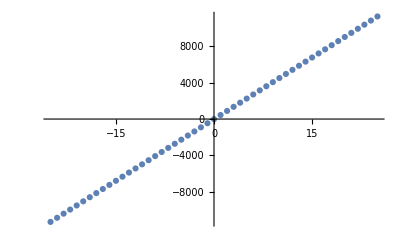

```mathematica
ListPlot[{Table[μ,{μ,-μmax,μmax}],ctable⟦;;,1⟧}ᵀ]
```

```mathematica
d1vec={}
d2vec={}
ω0svec={}
Do[coefs=CoefficientList[Fit[{Table[μ,{μ,-μmax,μmax}],ctable⟦;;,ii⟧}ᵀ,{1,x,x^2},x],x];
AppendTo[ω0svec,Re@coefs⟦1⟧];
AppendTo[d1vec,Re@coefs⟦2⟧];
AppendTo[d2vec,Re@coefs⟦3⟧];,{ii,1,3}]
ω0svec
d1vec
d2vec
```

{}

{}

{}

{-9.99824,0.441331,9.55691}

{451.854,451.857,451.841}

{-0.00799825,-0.00806392,-0.00510783}

```mathematica
ωb1=Eigenvalues[Ω][[2]]
ωb2=Eigenvalues[Ω][[1]]
ωb3=Eigenvalues[Ω][[3]]
```